# Coulb 1 Behavior Analysis Tests

## SPP026 141010

## Initial

```mathematica
<<PyonpyonW`
```

HokahokaW`
(origin)[https://ktakagaki@github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  24161a64fcfb50b8fa0954799b3d1b8272601b67
newest file:  Tue 14 Oct 2014 19:18:07

NounouW`
(origin)[https://ktakagaki@github.com/ktakagaki/NounouW.git]
current Git HEAD:  a9640024c05037332c61a2a21ebd1a15d04fda22
newest file:  Tue 14 Oct 2014 19:17:58

<<Set JLink` java stack size to 6144Mb>>

ParaparaW`
(origin)[https://ktakagaki@bitbucket.org/ktakagaki/paraparaw.git]
current Git HEAD:  0ec5fba69554c1305eecb95d7b8b3dcae15506a8
newest file:  Tue 14 Oct 2014 19:17:29

PyonpyonW`
(origin)[https://ktakagaki@bitbucket.org/ktakagaki/pyonpyonw.git]
current Git HEAD:  7fc6e2d2ae44e80b73a86176a0fdc653cae9fe40
newest file:  Tue 14 Oct 2014 19:18:47

```mathematica
coulb1Folder="U:\\VSDdata\\project.SPP\\SPP.Coulb1"(*\_arch"*);
nlx2Folder="U:\\VSDdata\\project.SPP\\SPP.Nlx2"(*\_arch"*);
subjectString="SPP026";
date={2014,10, 10};
```

```mathematica
{videoFile}=FileNames[FileNameJoin[{coulb1Folder,subjectString,
	ToString[date[[1]]]<>"-"<>ToString[date[[2]]]<>"-"<>ToString[date[[3]]]<>" *.wmv"}]]
```

{U:\VSDdata\project.SPP\SPP.Coulb1\SPP026\2014-10-10 16-33-03.503.wmv}

```mathematica
{nlxNevFile}=FileNames[FileNameJoin[{nlx2Folder,subjectString,ToString[date[[1]]]<>"-"<>ToString[date[[2]]]<>"-"<>ToString[date[[3]]]<>"*", "Events.nev"}]]
```

{U:\VSDdata\project.SPP\SPP.Nlx2\SPP026\2014-10-10_15-17-38\Events.nev}

## Import Events

```mathematica
{eventObj}=NNDataReader`load[nlxNevFile]
```

{«JavaObject[nounou.data.XEvents]»}

```mathematica
events=NNToList[eventObj];
```

### CSV and Ouptut For Troubleshooting

```mathematica
(*SortBy[events, #[[2]]&]//TableForm*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]];Export["Test_Coulb1_Analysis_SPP026.141010.tsv", ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events]*)
```

### Sorting

```mathematica
eventPorts=eventObj@ports[]
```

{0,100000000,100000001}

```mathematica
events0=Select[events,(#[[1]]==eventPorts[[1]])&];
events1=Select[events,(#[[1]]==eventPorts[[2]])&];
events2=Select[events,(#[[1]]==eventPorts[[3]])&];

events0= ReplacePart[#, 1->"Neuralynx"]& /@ events0;
events1= ReplacePart[#, 1->"Stimulus"]& /@ events1;
events2= ReplacePart[#, 1->"Colbourn"]& /@ events2;

Print["Neuralynx events: "<> ToString[Length[events0]]];
Print[events0//TableForm];
Print["Stimulus events: "<> ToString[Length[events1]]];
Print["Colbourne events: "<> ToString[Length[events2]]];
```

Neuralynx events: 2

Neuralynx | -9223372033667928359 | 0 | 0 | Starting Recording
Neuralynx | -9223372030316318359 | 0 | 0 | Stopping Recording

Stimulus events: 100

Colbourne events: 608

## Filter Out False Port Changes: Colbourn Bit Transition Bug (set new bits-then-unset old bits)

```mathematica
Dimensions[events2]
```

{608,5}

### Notes on the problem

Look at this crap ...
The Colbourn system always sets the new on bits (within one cycle, always, it seems), and then stepwise, goes through the new off bits, unsetting them one by one

-Graphics-

### Normalize Timing for Easier Display

```mathematica
events0=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events0;
events1=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events1;
events2=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events2;
```

### Correct Bit Transition Bug

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 3];
```

The following timestamps were removed: {}

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 2];
```

The following timestamps were removed: {1974333406, 2045681875, 2519092125, 2599866063}

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 1];
```

The following timestamps were removed: {214376938, 218911094, 229150281, 243859688, 253860500, 265630938, 270369938, 283700438, 296435188, 322943781, 345628625, 362038250, 365125344, 369648469, 391177281, 409462219, 414162063, 438356906, 460735781, 484625625, 516314750, 539864625, 544304688, 559136469, 567867969, 572488719, 598308594, 620832500, 643177375, 647672688, 672171313, 696966156, 713475750, 742749750, 747155000, 767239656, 788454531, 799298844, 813713344, 838248156, 867007250, 887757094, 892192813, 899871625, 912031906, 916166031, 917841219, 939610250, 943951031, 960937906, 965740781, 987164531, 1001764031, 1015769594, 1020273781, 1034624250, 1045053594, 1050168781, 1073577594, 1078813000, 1105172750, 1124741563, 1129246625, 1154156500, 1175940563, 1200445438, 1212128563, 1221788000, 1226650063, 1254639063, 1275773781, 1296228563, 1300924406, 1327082656, 1350012563, 1354471594, 1373026406, 1377621500, 1403176406, 1425950156, 1430476781, 1457399250, 1485079156, 1509388781, 1518623375, 1538348313, 1542808406, 1564237469, 1568692344, 1594472156, 1615180875, 1639136688, 1643467438, 1659310594, 1663685656, 1682598375, 1687529563, 1713454281, 1739033406, 1745265438, 1772247438, 1789757188, 1818317188, 1843841188, 1848347875, 1873361188, 1895299969, 1899730063, 1923998188, 1941723313, 1946563688, 1991973313, 1996478563, 2022082438, 2035267156, 2040268438, 2045681844, 2057592406, 2062162281, 2066611906, 2090850906, 2120135906, 2145045094, 2172833781, 2193028531, 2203039031, 2226930375, 2231721844, 2252712656, 2270162469, 2274459375, 2292497469, 2297116281, 2323851063, 2349255188, 2373699938, 2391244594, 2395844656, 2419233563, 2443878594, 2448328531, 2470512406, 2490502156, 2494922250, 2541600969, 2570785906, 2571240969, 2620279750, 2624989875, 2637644500, 2666233375, 2677198875, 2689178188, 2693958469, 2720632406}

### Correct Other Flow Irregularities

```mathematica
events2=PPCorrectColbournFlow[events2];
```

The following 3-trial sequences were removed: 
{{571868875, 6}, {572488688, 7}, {572488781, 13}}
{{746754906, 6}, {747154969, 7}, {747155063, 13}}
{{891762063, 6}, {892192781, 7}, {892192875, 13}}
{{916036000, 6}, {916166000, 7}, {916166125, 13}}
{{943610906, 6}, {943951000, 7}, {943951094, 13}}
{{1019773688, 6}, {1020273750, 7}, {1020273844, 13}}
{{1049061094, 6}, {1050168750, 7}, {1050168844, 13}}
{{1077589781, 6}, {1078812969, 7}, {1078813094, 13}}
{{1300232688, 6}, {1300924375, 7}, {1300924469, 13}}
{{1377031375, 6}, {1377621469, 7}, {1377621594, 13}}
{{1513392750, 6}, {1518623344, 7}, {1518623469, 13}}
{{1542353313, 6}, {1542808375, 7}, {1542808500, 13}}
{{1643139594, 6}, {1643467406, 7}, {1643467531, 13}}
{{1686601188, 6}, {1687529531, 7}, {1687529625, 13}}
{{1945724188, 6}, {1946563656, 7}, {1946563781, 13}}
{{1995978500, 6}, {1996478531, 7}, {1996478625, 13}}
{{2274167438, 6}, {2274459344, 7}, {2274459469, 13}}
{{2494507563, 6}, {2494922219, 7}, {2494922344, 13}}

The following 3-trial sequences were removed: 
{{218911188, 13}, {218916375, 9}, {218916406, 1}}
{{346583719, 13}, {346588938, 9}, {346588969, 1}}
{{747155063, 13}, {747160375, 9}, {747160406, 1}}
{{892192875, 13}, {892197406, 9}, {892197438, 1}}
{{916166125, 13}, {916171250, 9}, {916171281, 1}}
{{943951094, 13}, {943956500, 9}, {943956531, 1}}
{{988704531, 13}, {988709781, 9}, {988709813, 1}}
{{1020273844, 13}, {1020279000, 9}, {1020279031, 1}}
{{1050168844, 13}, {1050174031, 9}, {1050174063, 1}}
{{1078813094, 13}, {1078818000, 9}, {1078818031, 1}}
{{1129246719, 13}, {1129251813, 9}, {1129251844, 1}}
{{1201885094, 13}, {1201890406, 9}, {1201890438, 1}}
{{1354471688, 13}, {1354477406, 9}, {1354477438, 1}}
{{1377621594, 13}, {1377626719, 9}, {1377626750, 1}}
{{1518623469, 13}, {1518628719, 9}, {1518628750, 1}}
{{1542808500, 13}, {1542813625, 9}, {1542813656, 1}}
{{1568692438, 13}, {1568697531, 9}, {1568697563, 1}}
{{1643467531, 13}, {1643471188, 9}, {1643471219, 1}}
{{1663685750, 13}, {1663690906, 9}, {1663690938, 1}}
{{1687529625, 13}, {1687534969, 9}, {1687535000, 1}}
{{2066612000, 13}, {2066617563, 9}, {2066617594, 1}}
{{2274459469, 13}, {2274465188, 9}, {2274465219, 1}}
{{2395844750, 13}, {2395850000, 9}, {2395850031, 1}}
{{2448328625, 13}, {2448334156, 9}, {2448334188, 1}}
{{2494922344, 13}, {2494942500, 9}, {2494942531, 1}}
{{2693958563, 13}, {2693963813, 9}, {2693963844, 1}}

### Summary

```mathematica
Dimensions[events2]
```

{401,5}

```mathematica
Union[events2[[All, 4]]]
```

{1,2,3,4,5,6,7,8,9,13,63}

## Readouts for troubleshooting 141013

### Read out deleted events for troubleshooting 141013

```mathematica
speaker[number_]:=Module[{tempnum},
Speak["Next number"];
Speak[Quotient[number, 1000000]];
tempnum=Mod[number, 1000000];
Speak[Quotient[tempnum, 1000]];
tempnum=Mod[tempnum, 1000];
Speak[tempnum];
];
```

```mathematica
Speak["Hello"]
```

```mathematica
speaker/@ {438356906, 460735781, 484625625, 516314750, 539864625, 544304688, 559136469, 567867969, 572488719, 598308594, 620832500, 643177375, 647672688, 672171313, 696966156, 713475750, 742749750, 747155000, 767239656}
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{788454531, 799298844, 813713344, 838248156, 867007250, 887757094, 892192813, 899871625, 912031906, 916166031, 917841219, 939610250, 943951031, 960937906, 965740781, 987164531}
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1001764031, 1015769594, 1020273781, 1034624250, 1045053594, 1050168781}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1073577594, 1078813000, 1105172750, 1124741563, 1129246625, 1154156500, 1200445438}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 1212128563, 1221788000, 1226650063, 1254639063, 1275773781, 1296228563, 1300924406}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1327082656, 1350012563, 1354471594, 1373026406, 1377621500, 1403176406, 1425950156}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1430476781, 1457399250, 1485079156, 1509388781, 1518623375, 1538348313, 1542808406}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1564237469, 1568692344, 1594472156, 1615180875, 1639136688, 1643467438, 1659310594}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1663685656, 1682598375, 1687529563, 1713454281, 1739033406, 1745265438}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1772247438, 1789757188, 1818317188, 1843841188, 1848347875, 1873361188}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 1895299969, 1899730063, 1923998188, 1941723313, 1946563688, 1991973313}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 1996478563, 2022082438, 2035267156, 2040268438, 2045681844, 2057592406}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{2062162281, 2066611906, 2090850906, 2120135906, 2145045094, 2172833781}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2193028531, 2203039031, 2226930375, 2231721844, 2252712656, 2270162469}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2274459375, 2292497469, 2297116281, 2323851063, 2349255188, 2373699938}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2391244594, 2395844656, 2419233563, 2443878594, 2448328531, 2470512406}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2490502156, 2494922250, 2541600969, 2570785906, 2571240969, 2620279750}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2624989875, 2637644500, 2666233375, 2677198875, 2689178188, 2693958469, 2720632406}
```

{Null,Null,Null,Null,Null,Null,Null}

### Read out trials for troubleshooting 141013

```mathematica
SetDirectory[NotebookDirectory[]];
trials=Import["ppSessList.141010.1526.tsv"];
```

```mathematica
speakerTrial[list_List]:=
(Speak["New List"];
Speak /@ list);
```

```mathematica
Partition[trials[[1]],10]
```

{{1,1,1,2,2,2,1,2,1,2},{2,1,2,1,1,2,2,1,2,2},{1,1,2,1,2,2,2,1,1,1},{2,2,1,1,1,2,1,2,2,2},{1,2,2,1,2,1,1,2,1,2},{2,1,1,1,2,2,1,1,1,2},{1,2,1,2,1,2,1,2,1,2},{1,2,1,1,2,2,1,2,1,2},{2,1,1,2,1,2,1,2,1,2},{1,1,1,2,2,2,1,2,1,2}}

```mathematica
speakerTrial /@ %;
```

## Check for jumps and annotate with side

```mathematica
events2=ReplaceRepeated[events2, 
{head___, 
{"Colbourn", x2_,0, x4_, xx__},
{"Colbourn", y2_,0, y4_, yy__}, 
tail___}/;(MemberQ[{6,8,12},x4] && y4==1 &&(y2-x2)<4010000) 
-> 
{head, {"Colbourn", x2,0, x4, xx},{"Colbourn", y2, 0, x4+300, "Added to troubleshoot jump registration in early script. "},{"Colbourn", y2, 0, y4, yy}, tail}
];
```

```mathematica
(*Nothing should be changed here for experiments after late 8/2014*)
Dimensions[events2]
```

{402,5}

```mathematica
tempLastJumpToParity=False;
tempLastJumpToParityTrueIsSw1=Null;
eventJumpAnnotator[event_]:=
Module[{},
If[event[[1]]==="Colbourn",
Switch[event[[4]],
2, (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=tempLastJumpToParity];
If[Xor[tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump]
]),
3, (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=!tempLastJumpToParity];
If[Xor[!tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump]
]),
x_/;MemberQ[{5,8,13,306,308,305,309},x], tempLastJumpToParity=!tempLastJumpToParity,
_, Null]
];
Join[event,{tempLastJumpToParity}]
];
eventJumpAnnotator::parityJump="It seems that a jump was not registered!";
```

```mathematica
(*tempPrintVar=eventsCoulb[[1,2]];
(Print[Join[eventJumpAnnotator[#],{#[[2]]-tempPrintVar}]];tempPrintVar=#[[2]];)& /@ eventsCoulb;*)
```

```mathematica
events2=eventJumpAnnotator/@ events2;
```

```mathematica
events2=events2 //. If[tempLastJumpToParityTrueIsSw1, {True->"Sw1", False->"Sw2"},{True->"Sw2", False->"Sw1"}];
```

## Separate into trials

```mathematica
trialStartTimes=Cases[events2,{"Colbourn", _, 0, x_/;MemberQ[{4,7,10}, x],__}][[All, 2]];
Length[trialStartTimes]
```

101

```mathematica
eventsAll=SortBy[Join[ Append[#,"XXX"]& /@events0, Append[#,"XXX"]& /@events1,events2],#[[2]]&];
Dimensions[eventsAll]
```

{504,6}

```mathematica
selectTrials[{trialTimes_, trialTimesNext_}]:=
Select[eventsAll,
((trialTimes-5000000)<#[[2]]&& #[[2]]<Min[trialTimesNext-5000000, trialTimes+30000000])&]
```

```mathematica
trialsColb=selectTrials/@ Partition[Append[trialStartTimes,Infinity],2,1];
Dimensions[trialsColb]
```

{101}

## Plot Trial Graph

```mathematica
PPPlotTrialImplArrow[trialElement_List]:=
{If[MemberQ[{2,3,13,5,8,11},trialElement[[4]]]&&trialElement[[6]]==="Sw1", Arrow[{{trialElement[[2]]/1000,-50},{trialElement[[2]]/1000,50}}],
If[MemberQ[{2,3,13,5,8,11},trialElement[[4]]]&&trialElement[[6]]==="Sw2", Arrow[{{trialElement[[2]]/1000,50},{trialElement[[2]]/1000,-50}}],
Line[{{trialElement[[2]]/1000,-50},{trialElement[[2]]/1000,50}}]
]],
Text[trialElement[[4]],  {trialElement[[2]]/1000, 50}, BaseStyle->{FontWeight->"Normal", FontSize->12}]
};
```

```mathematica
PPPlotTrial[trial_]:=
Module[{trialNum,trialsStim,trialsStimDAQ, trialSub,
tempStimCode,tempShockRange, trialJumps,tempgr},

trialsStim=PPColbournTrialGetStimulus[trial];
trialsStimDAQ=Select[trial, #[[1]]==="Stimulus"&];

(*Print["Colbourn Trigger Timestamp: "<> ToString[trialsStim[[2]]]];*)
(*Print[trial//TableForm];*)
trialSub=ReplacePart[#, 2->(#[[2]]-trialsStim[[2]])]&/@Select[trial,#[[1]]==="Colbourn"&];
trialsStimDAQ=ReplacePart[#, 2->(#[[2]]-trialsStim[[2]])]& /@trialsStimDAQ;

trialNum=If[PPPlotTrialNumber===Null,"","Trial "<>ToString[PPPlotTrialNumber += 1]<>": "]; 

tempgr= Graphics[
{{(*Caption*)
Black,
Text[
trialNum <> PPColbournTrialGetType[trial]<>" trial ("<>
ToString[PPColbournTrialGetStartingTime[trial]]<>")",  
{-5000, 100},{-1,1}, BaseStyle->{FontWeight->"Bold", FontSize->12}]
},
{(*Stimulus rectangle*)
Opacity[0.25,Black],
Rectangle[{#[[2]]/1000,-80},{(#[[2]]+#[[3]])/1000,80}]& /@ trialsStimDAQ
},
{(*Shock rectangle*)
tempShockRange=PPColbournTrialGetShockRange[trialSub];
If[tempShockRange=={},{},
{Opacity[0.5,Yellow],
Rectangle[{tempShockRange[[1]]/1000,-80},{tempShockRange[[2]]/1000,80}]}
]
},
{(*Stimulus code*)
If[EvenQ[tempStimCode=PPColbournTrialGetStimulusDAQCode[trial]],Darker[Red],Darker[Green]],
Text[tempStimCode,  {0, 50}, BaseStyle->{FontWeight->"Bold", FontSize->15}]
},
{(*Trial Start*)
},
{(*Jumps*)
trialJumps=Select[trialSub, MemberQ[{2,3,13,5,6,8,9,11,12,306,308,305,309},#[[4]]]&];
Black,Arrowheads[Medium],
PPPlotTrialImplArrow /@ trialJumps
}
}, Axes->{True, False},GridLinesStyle->LightBlue,GridLines->{{0,4000, 6000},None}];

Print[Show[tempgr,
PlotRange->{{-5000, 25000},{-100, 100}},AspectRatio->1/10,
ImageSize->72*10,
Ticks->{Range[-4000,24000,2000],None}]]
(*Print[Show[tempgr,
PlotRange->{{10000, 25000},{-100, 100}},AspectRatio->1/10,
Ticks->{Range[12000,24000,2000],None}]];*)
];
```

```mathematica
PPColbournTrialGetStartingSide/@trialsColb
```

```mathematica
PPColbournTrialGetType/@trialsColb
```

```mathematica
PPColbournTrialGetShockRange/@trialsColb
```

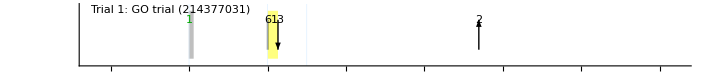

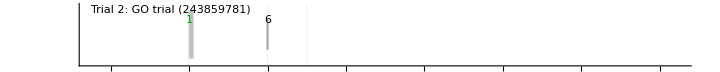

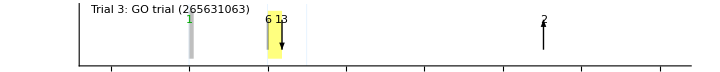

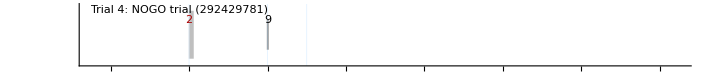

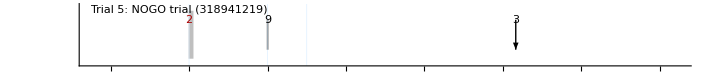

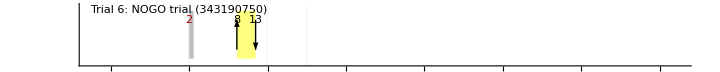

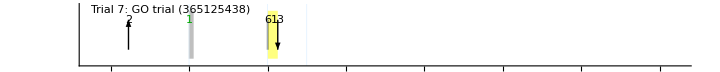

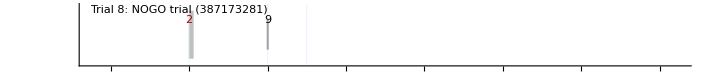

Part::partw: Part 4 of Missing["NotFound"] does not exist.

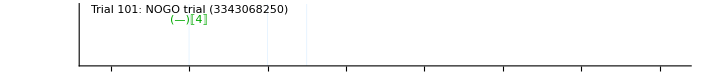

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
PPPlotTrialNumber=0;
PPPlotTrial /@ trialsColb
```

```mathematica
Length[trialsColb]
```

101

```mathematica
trialsColb[[1]]
```

{{Stimulus,214363344,249781,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},{Colbourn,214377031,0,4,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).,Sw1},{Colbourn,218381063,0,6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).,Sw1},{Colbourn,218911188,0,13,TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).,Sw2},{Colbourn,218916406,0,1,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).,Sw2},{Colbourn,229150375,0,2,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).,Sw1}}

## Import Video and Align